# Measure of Center

The center of a distribution is a typical value that represents the group. We will discuss how the shape of the distribution might influence whether the mean is larger than, smaller than, or about the same as the median.

## Observations

Let’s take a look at the salaries from three university campuses.

View the data:

```mathematica
ResourceData["Sample Data: University Salaries"]
```

Dataset[<>]

We can see the salaries by department.

Organize the data by department:

```mathematica
data=GroupBy[ResourceData["Sample Data: University Salaries"], "Department"][All, All, "Salary"]
```

Dataset[<>]

Let’s take a look at the distribution of the salaries of the Surgery department, which is #2 in the data.

Make a histogram of 112 salaries of the Surgery department in the data:

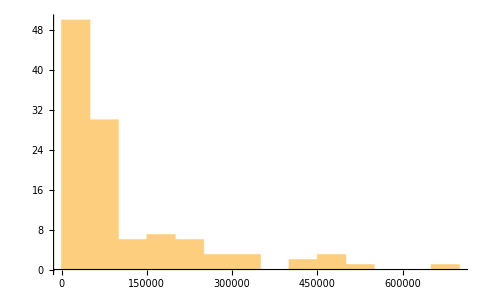

```mathematica
d=2;
hist=Histogram[data[[d]]]
```

The shape of the salaries distribution of the Surgery department is skew-right. The mean of the salaries of the Surgery department is affected by the outlier $650,000 per year.

This finds the mean of the salaries:

```mathematica
mean=QuantityMagnitude[Mean[data[[d]]]]
```

106748.

Is this a good estimate of the center of this distribution? Let’s take a look at the median.

This finds the median of the salaries:

```mathematica
median=QuantityMagnitude[Median[data[[d]]]]
```

51038.2

Which one is a better estimate of the center of this distribution?

Show the histogram, mean, and median together:

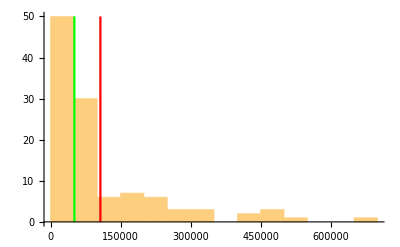

```mathematica
Show[hist,ContourPlot[{x==mean},{x,mean-1,mean+1},{y,0,50},ContourStyle->Red,ColorFunction->Automatic,Frame->False,Axes->True],ContourPlot[{x==median},{x,median-1,median+1},{y,0,50},ContourStyle->Green,ColorFunction->Automatic,Frame->False,Axes->True]]
```

## Deciding Which Measurements to Use

### Skewed-Right Distributions

We now have a choice between two measurements of center and spread. We can use the median with the interquartile range, or we can use the mean with the standard deviation. Our next examples show that the shape of the distribution and the presence of outliers helps us to decide which measurements to use.

Here are the salaries distributions for the first 10 departments:

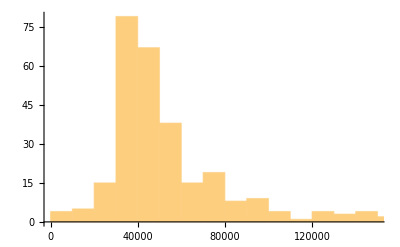
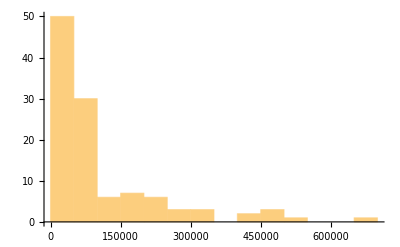
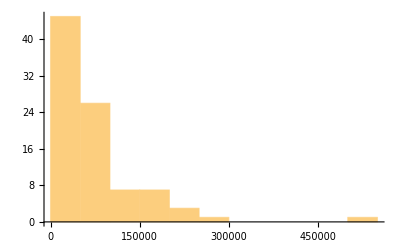
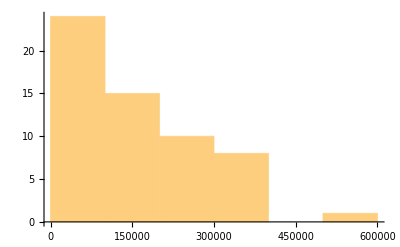
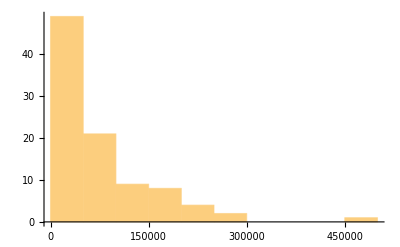
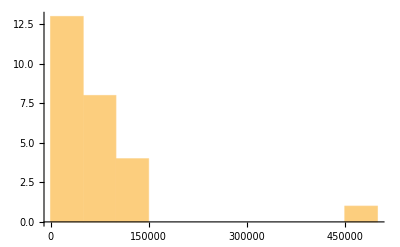
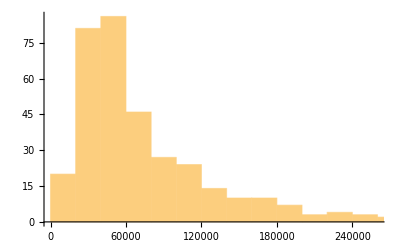
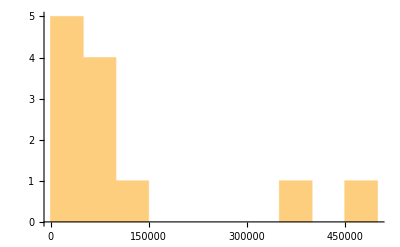

```mathematica
Table[Histogram[data[[i]]],{i,10}]
```

We see that the median represents the typical income of people in this sample better than the mean. The small number of people with higher incomes does not impact the median or the other quartile marks, so the first and third quartile marks give a range of incomes that more accurately represent typical incomes in the sample.

Let’s take a look at the first histogram, except this time we overlay a boxplot:

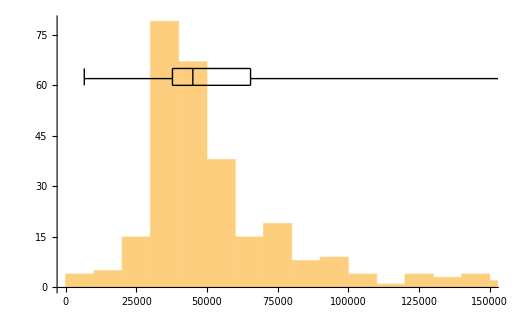

```mathematica
min=QuantityMagnitude[Min[data[[1]]]];
q1=QuantityMagnitude[Quantile[Normal[data[[1]]],.25]];
q2=QuantityMagnitude[Median[data[[1]]]];
q3=QuantityMagnitude[Quantile[Normal[data[[1]]],.75]];
max=QuantityMagnitude[Max[data[[1]]]];
Histogram[data[[1]],Epilog->{
Line[{{min,60},{min,65}}],
Line[{{q1,60},{q1,65}}],
Line[{{q2,60},{q2,65}}],
Line[{{q3,60},{q3,65}}],
Line[{{max,60},{max,65}}],
Line[{{q1,65},{q3,65}}],
Line[{{q1,60},{q3,60}}],
Line[{{min,62},{q1,62}}],
Line[{{q3,62},{max,62}}]
 }]
```

### Skewed-Left Distributions

We take a look at the test scores of two exams given by a easy grader and a tough grader.

```mathematica
data1={33,46,55,59,68,70,72,75,78,78,79,80,80,82,85,89,90,94,95}; 
data2={0,5,8,12,20,23,24,25,32,40,42,48,48,49,50,52,55,64,70,70,73,80};
```

Combine the boxplot and histogram of the scores in one plot:

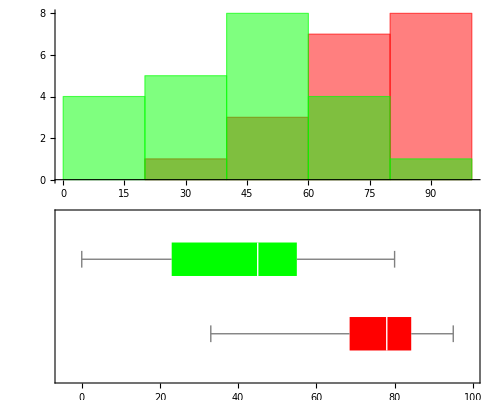

```mathematica
hist=Histogram[{data1,data2},ChartStyle->{Red,Green}];
bxchrt=BoxWhiskerChart[{data1,data2},BarOrigin->Left,AspectRatio->1/4,ChartStyle->{Red,Green},PlotRangePadding->None];
plotGrid[{{hist},{bxchrt}},500,400]
```

In a skewed distribution, the upper half and the lower half of the data have a different amount of spread, so no single number such as the standard deviation could describe the spread very well. We get a better understanding of how the values are distributed if we use the quartiles and the two extreme values in the five-number summary.

### Symmetric Distributions

Use the mean and the standard deviation as measures of center and spread only for distributions that are reasonably symmetric with a central peak.

The distribution of baby weight is reasonably symmetric with a central peak. It has a mean of 7.78 lb with standard deviation of 0.66 lb:

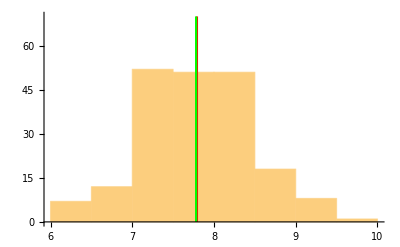

```mathematica
baby=RandomVariate[NormalDistribution[7.78,0.66],200];
mean=Mean[baby];
median=Median[baby];
histb=Histogram[baby];
Show[histb,ContourPlot[{x==mean},{x,mean-.1,mean+.1},{y,0,70},ContourStyle->Red,ColorFunction->Automatic,Frame->False,Axes->True],ContourPlot[{x==median},{x,median-.1,median+.1},{y,0,70},ContourStyle->Green,ColorFunction->Automatic,Frame->False,Axes->True]]
```

When outliers are present, the mean and standard deviation are not a good choice.

When there are premature babies present in the above data set:

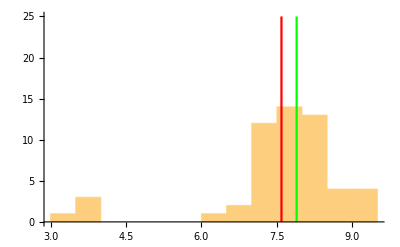

```mathematica
baby2=Join[RandomVariate[NormalDistribution[7.78,0.66],50],{3.3,3.6,3.8,3.5}];
mean2=Mean[baby2];
median2=Median[baby2];
histb2=Histogram[baby2];
Show[histb2,ContourPlot[{x==mean2},{x,mean2-.1,mean2+.1},{y,0,25},ContourStyle->Red,ColorFunction->Automatic,Frame->False,Axes->True],ContourPlot[{x==median2},{x,median2-.1,median2+.1},{y,0,25},ContourStyle->Green,ColorFunction->Automatic,Frame->False,Axes->True]]
```

## Summary

Use the mean as a measure of center only for distributions that are reasonably symmetric with a central peak. When outliers are present, the mean is not a good choice.

Use the median as a measure of center for all other cases.

Here is a manipulation to illustrate this guideline:

```mathematica
Manipulate[
Module[{distribution,qlo,qhi,m,Q1,Q3,mu,ym,yQ1,yQ3,ymu},
distribution=Switch[d,
1,GammaDistribution[a,1],
2,BetaDistribution[a+1/2,1]
];
qlo=Quantile[distribution,0.001];
qhi=Quantile[distribution,0.999];
m=Median[distribution];
Q1=Quantile[distribution,0.25];
Q3=Quantile[distribution,0.75];
mu=Mean[distribution];
ym=PDF[distribution,m];
yQ1=PDF[distribution,Q1];
yQ3=PDF[distribution,Q3];
ymu=PDF[distribution,mu];
Plot[PDF[distribution,x],{x,qlo,qhi},
PlotRange→All,Filling→0,FillingStyle→LightGray,AxesOrigin→{0,0},
PlotLabel→Row[{Style["mean",Red], " and ", Style["median",Green]}],
Epilog→{
Red,
Line[{{mu,0},{mu,ymu}}],
Text[Style["μ",16],{mu,ymu},{0,1},{1,1}],
Green,
Line[{{m,0},{m,ym}}],
Text[Style["m",Italic,16],{m,ym},{0,1},{1,1}]
},
ImageSize→{500,300}
]],
{a,1.1,20,Appearance→"Labeled"},
{{d,1,"distribution"},{1→ "Right Skewed",2→"Left Skewed"}},
TrackedSymbols:>{a,d}]
```

## Exercises

In many practical situations we are interested in measuring how many times a certain event occurs in a specific time interval or in a specific length or area. For instance: the number of texts students received during class in an hour.

What is a better measure of the center of this distribution, mean or median?

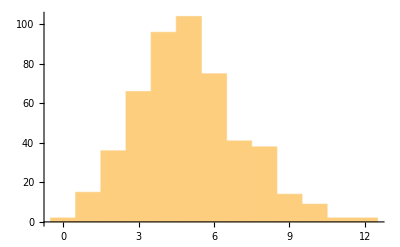

```mathematica
data=RandomVariate[PoissonDistribution[5],500];
hist=Histogram[data]
MessageDialog["Create a timed-game for students to hit mean or median on different randomly generated datasets in the background."];
```

What if we are not given the histogram of the distribution?

How do we decide the better measure of center?

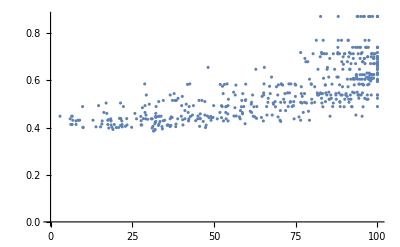

```mathematica
ListPlot[ResourceData["Sample Data: Boston Homes"][All, {"AGE", "NOX"}]]
```

Further Explorations

Investigate the website datarepository.wolframcloud.com and explain your choice of measure of center for a dataset that you are interested in.

## Initialization

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]];
```

Authorship information

Jie Frye

June 20, 2017

jiefrye@gmail.com